```mathematica
SetDirectory[NotebookDirectory[]]
relevant=Select[Union[Import["/Users/hayssam/Documents/ISOP_0.2/tests/relevant_documents.tsv"]],#[[4]]=="False"&];
relevant=Select[relevant,Length[#]==75&];
bySeed=GatherBy[relevant,#[[7]]&];
Length[relevant]
```

/Users/hayssam/Documents/ISOP_0.2/tests

2807

```mathematica
Union[relevant[[All,{1,2,3,4,8,9}]]]//MatrixForm
nMethods=Length[%]
```

(True | False | True | False | XAP | 100)

1

```mathematica
pathways=Union[relevant[[All,5]]]
```

{2,4,7,9,11,14}

```mathematica
Length[relevant[[-1]]]
```

75

```mathematica
r1=relevant[[1]]
r2=relevant[[2]]
r1[[7]]==r2[[7]]
Partition[Partition[Riffle[r1[[10;;]],r2[[10;;]]],2],3]//MatrixForm
```

{True,False,True,False,2,1,{10075738},XAP,100,1,1.,0.01,51,0.41,0.25,101,0.33,0.4,151,0.3,0.55,201,0.32,0.77,251,0.3,0.9,301,0.26,0.95,351,0.23,0.95,401,0.2,0.96,451,0.18,0.98,501,0.16,0.99,551,0.15,0.99,601,0.14,1.,651,0.13,1.,701,0.12,1.,751,0.11,1.,801,0.1,1.,851,0.1,1.,901,0.09,1.,951,0.09,1.,1001,0.08,1.,1051,0.08,1.}

{True,False,True,False,2,1,{10085091},XAP,100,1,1.,0.01,51,0.33,0.2,101,0.26,0.31,151,0.3,0.55,201,0.29,0.7,251,0.29,0.89,301,0.26,0.94,351,0.23,0.96,401,0.2,0.96,451,0.18,0.96,501,0.16,0.96,551,0.15,0.98,601,0.14,0.99,651,0.13,0.99,701,0.12,1.,751,0.11,1.,801,0.1,1.,851,0.1,1.,901,0.09,1.,951,0.09,1.,1001,0.08,1.,1051,0.08,1.}

False

((1
1) | (1.
1.) | (0.01
0.01)
(51
51) | (0.41
0.33) | (0.25
0.2)
(101
101) | (0.33
0.26) | (0.4
0.31)
(151
151) | (0.3
0.3) | (0.55
0.55)
(201
201) | (0.32
0.29) | (0.77
0.7)
(251
251) | (0.3
0.29) | (0.9
0.89)
(301
301) | (0.26
0.26) | (0.95
0.94)
(351
351) | (0.23
0.23) | (0.95
0.96)
(401
401) | (0.2
0.2) | (0.96
0.96)
(451
451) | (0.18
0.18) | (0.98
0.96)
(501
501) | (0.16
0.16) | (0.99
0.96)
(551
551) | (0.15
0.15) | (0.99
0.98)
(601
601) | (0.14
0.14) | (1.
0.99)
(651
651) | (0.13
0.13) | (1.
0.99)
(701
701) | (0.12
0.12) | (1.
1.)
(751
751) | (0.11
0.11) | (1.
1.)
(801
801) | (0.1
0.1) | (1.
1.)
(851
851) | (0.1
0.1) | (1.
1.)
(901
901) | (0.09
0.09) | (1.
1.)
(951
951) | (0.09
0.09) | (1.
1.)
(1001
1001) | (0.08
0.08) | (1.
1.)
(1051
1051) | (0.08
0.08) | (1.
1.))

```mathematica
Length/@GatherBy[relevant,#[[;;4]]&]
```

{2807}

```mathematica
bySeed[[1]]
```

{{True,False,True,False,2,1,{10075738},XAP,100,1,1.,0.01,51,0.41,0.25,101,0.33,0.4,151,0.3,0.55,201,0.32,0.77,251,0.3,0.9,301,0.26,0.95,351,0.23,0.95,401,0.2,0.96,451,0.18,0.98,501,0.16,0.99,551,0.15,0.99,601,0.14,1.,651,0.13,1.,701,0.12,1.,751,0.11,1.,801,0.1,1.,851,0.1,1.,901,0.09,1.,951,0.09,1.,1001,0.08,1.,1051,0.08,1.}}

```mathematica
RowMethod[row_]:=row[[{8,9,1,2,3,4}]]
Offsets[row_]:= row[[Range[10,Length[row],3]]]
Precisions[row_]:= row[[Range[11,Length[row],3]]]
Recalls[row_]:= row[[Range[12,Length[row],3]]]
Pathway[row_]:=row[[5]]
QuerySize[row_]:=row[[6]]
PrecPlot[row_]:=ListLinePlot[Partition[Riffle[Offsets[row],Precisions[row]],2]]
RecallPlot[row_]:=ListLinePlot[Partition[Riffle[Offsets[row],Recalls[row]],2],PlotRange->{{0,1100},{0,1.1}},PlotStyle->If[row[[8]]=="LSI",{Black},{Red}]]
PrecRecallPlot[row_]:=
ListLinePlot[Partition[Riffle[Recalls[row],Precisions[row]],2],PlotRange->{{0,1.1},{0,1.1}},PlotStyle->If[row[[8]]=="LSI",{Black},{Red}]]
```

```mathematica
r=relevant[[2]]
```

{True,False,True,False,2,1,{10085091},XAP,100,1,1.,0.01,51,0.33,0.2,101,0.26,0.31,151,0.3,0.55,201,0.29,0.7,251,0.29,0.89,301,0.26,0.94,351,0.23,0.96,401,0.2,0.96,451,0.18,0.96,501,0.16,0.96,551,0.15,0.98,601,0.14,0.99,651,0.13,0.99,701,0.12,1.,751,0.11,1.,801,0.1,1.,851,0.1,1.,901,0.09,1.,951,0.09,1.,1001,0.08,1.,1051,0.08,1.}

{XAP,100,True,False,True,False}

{1,51,101,151,201,251,301,351,401,451,501,551,601,651,701,751,801,851,901,951,1001,1051}

2

{1.,0.33,0.26,0.3,0.29,0.29,0.26,0.23,0.2,0.18,0.16,0.15,0.14,0.13,0.12,0.11,0.1,0.1,0.09,0.09,0.08,0.08}

{0.01,0.2,0.31,0.55,0.7,0.89,0.94,0.96,0.96,0.96,0.96,0.98,0.99,0.99,1.,1.,1.,1.,1.,1.,1.,1.}

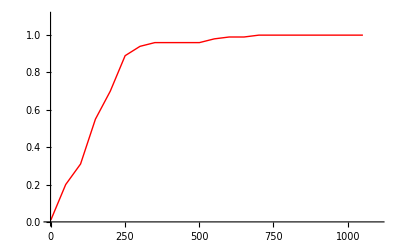

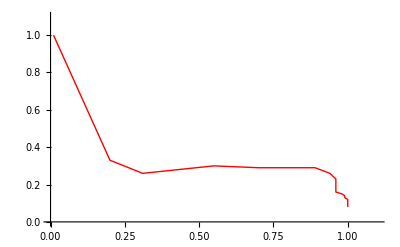

```mathematica
RowMethod[r]
Offsets[r]
Pathway[r]
Precisions[r]
Recalls[r]
RecallPlot[r]
PrecRecallPlot[r]
```

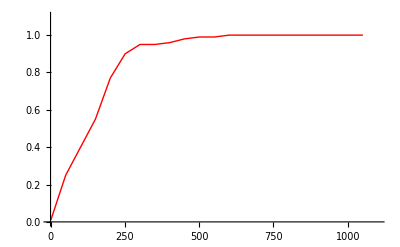
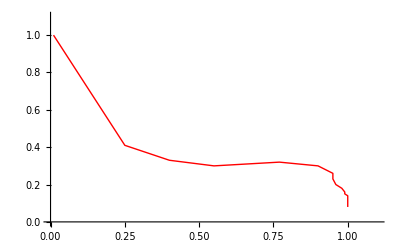
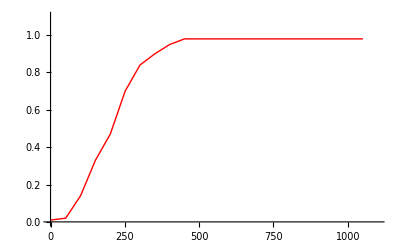
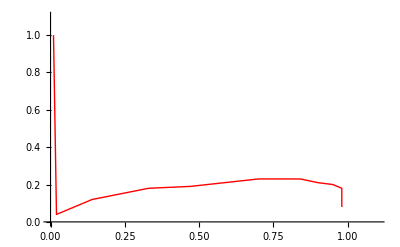
{{XAP,100,True,False,True,False}} | {2} | {1} | -Graphics- | -Graphics-
{{XAP,100,True,False,True,False}} | {2} | {1} | -Graphics- | -Graphics-
{{XAP,100,True,False,True,False}} | {2} | {1} | -Graphics- | -Graphics-

```mathematica
Grid[
{RowMethod/@ #,
Pathway/@#,
QuerySize/@#,
Show[RecallPlot/@#],
Show[PrecRecallPlot/@#]
}&/@bySeed[[1;;3]]
]
```

```mathematica
byPw=GatherBy[relevant,Pathway];
```

```mathematica
Manipulate[
With[{rows=bySeed[[i]]},
{Pathway[rows[[1]]],QuerySize[rows[[1]]],Show[RecallPlot/@rows]}]
,{i,1,Length[bySeed],1}
]
```

Part::partd: Part specification bySeed ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification RecallPlot[1] is neither an integer nor a list of integers.

Show::gtype: Part is not a type of graphics.

## Comparing precision/recall at 200 documents

```mathematica
Union[relevant[[All,{5,6}]]]
```

{{2,1},{2,2},{2,5},{2,8},{2,10},{2,16},{2,41},{2,62},{4,1},{4,2},{4,5},{4,8},{4,10},{4,16},{4,41},{4,62},{7,1},{7,2},{7,5},{7,8},{7,10},{7,16},{7,41},{7,62},{9,1},{9,2},{9,5},{9,8},{9,10},{9,16},{9,41},{9,62},{11,1},{11,2},{11,5},{11,8},{11,10},{11,16},{11,41},{11,62},{14,1},{14,2},{14,5},{14,8},{14,10},{14,16},{14,41},{14,62}}

```mathematica
pw=4;
querySize=2;
thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod];
Dimensions[thisRelevant]
```

{1,60,75}

Part::partw: Part 2 of {{{"True", "False", "True", "False", 4, 2, "{10075741,11956154}", "XAP", 100, 1, 1., 0.01, 51, 0.22, 0.07, 101, 0.26, 0.17, 151, 0.25, 0.24, 201, 0.24, 0.31, 251, 0.24, 0.39, 301, 0.22, 0.42, 351, 0.22, 0.5, 401, 0.22, 0.57, 451, 0.21, 0.61, 501, 0.19, 0.63, 551, 0.18, 0.64, 601, 0.16, 0.65, 651, 0.16, « 25 »}, {"True", "False", "True", "False", 4, 2, "{10090765,12628925}", "XAP", 100, 1, 1., 0.01, 51, 0.12, 0.04, 101, 0.07, 0.05, 151, 0.05, 0.05, 201, 0.04, 0.05, 251, 0.04, 0.06, 301, 0.03, 0.07, 351, 0.03, 0.07, 401, 0.03, 0.08, 451, 0.03, 0.08, 501, 0.03, 0.08, 551, 0.02, 0.08, 601, 0.02, 0.08, 651, 0.02, « 25 »}, « 48 », « 10 »}} does not exist.

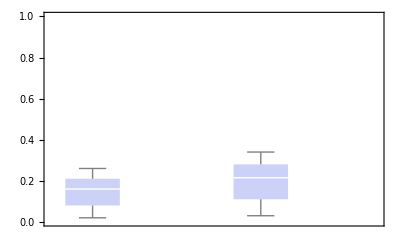

```mathematica
prec200lsi=thisRelevant[[1,All,23]];
rec200lsi=thisRelevant[[1,All,24]];
prec200xap=thisRelevant[[2,All,23]];
rec200xap=thisRelevant[[2,All,24]];
BoxWhiskerChart[{prec200lsi,prec200xap,rec200lsi,rec200xap},PlotRange->{{0,6},{0,1}}]
```

```mathematica
TTest[{prec200lsi,prec200xap},Automatic,"TestConclusion"]
TTest[{rec200lsi,rec200xap},Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5. percent level based on the T test.

The null hypothesis that the mean difference is 0 is not rejected at the 5. percent level based on the T test.

## Stacking prec box / whisker as a function of query size

```mathematica
Table[{relevant[[1,i]],{"prec",i+1,"reC",i+2}},{i,Range[10,75,3]}]//MatrixForm
```

(1 | {prec,11,reC,12}
51 | {prec,14,reC,15}
101 | {prec,17,reC,18}
151 | {prec,20,reC,21}
201 | {prec,23,reC,24}
251 | {prec,26,reC,27}
301 | {prec,29,reC,30}
351 | {prec,32,reC,33}
401 | {prec,35,reC,36}
451 | {prec,38,reC,39}
501 | {prec,41,reC,42}
551 | {prec,44,reC,45}
601 | {prec,47,reC,48}
651 | {prec,50,reC,51}
701 | {prec,53,reC,54}
751 | {prec,56,reC,57}
801 | {prec,59,reC,60}
851 | {prec,62,reC,63}
901 | {prec,65,reC,66}
951 | {prec,68,reC,69}
1001 | {prec,71,reC,72}
1051 | {prec,74,reC,75})

```mathematica
pw=7;
querySizes=Union[Select[relevant,#[[5]]==pw&][[All,6]]]
```

{1,2,5,10,13,27,68,102}

```mathematica
DistribPrecForPwSize[pw_,querySize_]:=With[{thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod]},
#[[1,{6,8,9,1,2,3}]]->#[[All,20]]&/@thisRelevant
]
DistribRecForPwSize[pw_,querySize_]:=With[{thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod]},
#[[1,{6,8,9,1,2,3}]]->#[[All,21]]&/@thisRelevant
]
```

```mathematica
TagForMethods[m_]:= 
ToString[m[[1]]]<>" q, "<>
m[[2]]<> "\n"<>
If[m[[3]]=="True","G",If[m[[3]]==-1,"G+","¬G"]]<>" "<>
If[m[[4]]=="True","M","¬M"]<>" "<>
If[m[[5]]=="True","S","¬S"]
```

```mathematica
TagForMethods[m_]:= 
Style[Grid[Transpose[{{m[[1]], m[[2]], m[[3]]}, {Switch[m[[4]],"False","",-1,"G+","True","G",_,"G"<>ToString[m[[4]]]], If[m[[5]]=="True","M",""], If[m[[6]]=="True","S",""]}}],Frame->LightGray],FontSize->8]
TagForMethods[{1,"LSI",250,"True","True","True"}]
```

1 | G
LSI | M
250 | S

```mathematica
pw=7;
val=DistribRecForPwSize;
d=Join[
val[pw,1],
(*val[pw,2],*)
(*val[pw,5]*)
val[pw,querySizes[[-3]]],
val[pw,querySizes[[-1]]]
];
d=Sort[d];
```

```mathematica
d
```

{{1,XAP,100,True,False,True}→{0.32,0.31,0.26,0.44,0.12,0.4,0.36,0.03,0.38,0.27,0.36,0.28,0.03,0.4,0.07,0.04,0.36,0.32,0.2,0.17,0.4,0.42,0.08,0.17,0.23,0.41,0.12,0.31,0.22,0.35,0.33,0.38,0.31,0.23,0.41,0.34,0.32,0.07,0.25,0.07,0.07,0.02,0.42,0.34,0.18,0.28,0.32,0.31,0.41},{27,XAP,100,True,False,True}→{0.43,0.44,0.44,0.41,0.42,0.44,0.43,0.42,0.43,0.43,0.43,0.42,0.42,0.42,0.43,0.42,0.41,0.43,0.45,0.45,0.43,0.46,0.42,0.43,0.41,0.45,0.43,0.44,0.41,0.43,0.44,0.44,0.43,0.41,0.46,0.42,0.42,0.41,0.45,0.41,0.45,0.42,0.41,0.42,0.45,0.45,0.45,0.45,0.45,0.46,0.44,0.45,0.42,0.45,0.4,0.45,0.44,0.42,0.45,0.45},{102,XAP,100,True,False,True}→{0.44,0.45,0.45,0.44,0.44,0.45,0.45,0.44,0.44,0.44,0.45,0.44,0.44,0.45,0.44,0.42,0.44,0.43,0.44,0.44,0.44,0.44,0.45,0.45,0.44,0.44,0.44,0.43,0.44,0.45,0.44,0.43,0.44,0.44,0.44,0.41,0.43,0.44,0.44,0.44,0.44,0.45,0.45,0.42,0.45,0.45,0.44,0.44,0.44,0.44,0.44,0.45,0.44,0.45,0.44,0.45,0.45,0.45,0.44,0.44}}

```mathematica
Mean /@ d[[1,2]]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[0.32].

Mean::rectt: Rectangular array expected at position 1 in Mean[0.31].

Mean::rectt: Rectangular array expected at position 1 in Mean[0.26].

General::stop: Further output of Mean :: rectt will be suppressed during this calculation.

{Mean[0.32],Mean[0.31],Mean[0.26],Mean[0.44],Mean[0.12],Mean[0.4],Mean[0.36],Mean[0.03],Mean[0.38],Mean[0.27],Mean[0.36],Mean[0.28],Mean[0.03],Mean[0.4],Mean[0.07],Mean[0.04],Mean[0.36],Mean[0.32],Mean[0.2],Mean[0.17],Mean[0.4],Mean[0.42],Mean[0.08],Mean[0.17],Mean[0.23],Mean[0.41],Mean[0.12],Mean[0.31],Mean[0.22],Mean[0.35],Mean[0.33],Mean[0.38],Mean[0.31],Mean[0.23],Mean[0.41],Mean[0.34],Mean[0.32],Mean[0.07],Mean[0.25],Mean[0.07],Mean[0.07],Mean[0.02],Mean[0.42],Mean[0.34],Mean[0.18],Mean[0.28],Mean[0.32],Mean[0.31],Mean[0.41]}

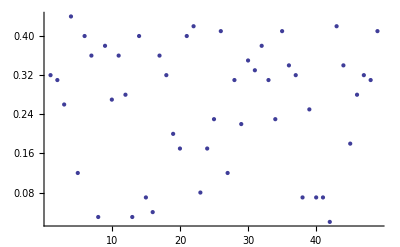

```mathematica
ListPlot[d[[1,2]]]
```

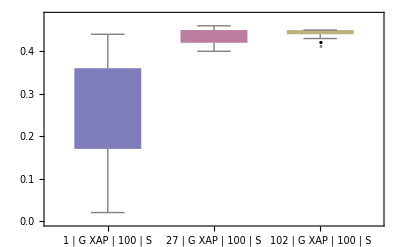

```mathematica
BoxWhiskerChart[
d[[All,2]],"Outliers",
ChartStyle->
Table[
If[d[[i,1,2]]=="XAP",
Lighter[ColorData[1,"ColorList"][[Floor[(i-1)/(nMethods)]+1]]],
Darker[ColorData[1,"ColorList"][[Floor[(i-1)/(nMethods)]+1]]]
],{i,1,Length[d]}],
ChartLabels->(TagForMethods[#[[1]]]&/@ d),
PlotRange->{Automatic,Automatic},
ImageSize->Full]
```

```mathematica
val[pw,10]
```

{{10,LSI,500,-1,False,True}→{0.56,0.54,0.53,0.52,0.53,0.58,0.49,0.56,0.55,0.57,0.55,0.59,0.53,0.55,0.55,0.53,0.57,0.55,0.53,0.52,0.5,0.56,0.58,0.56,0.54,0.55,0.55,0.55,0.56,0.53},{10,LSI,500,2,False,True}→{0.59,0.55,0.57,0.51,0.55,0.6,0.53,0.56,0.57,0.59,0.58,0.59,0.59,0.58,0.6,0.52,0.59,0.57,0.55,0.51,0.56,0.58,0.58,0.56,0.57,0.56,0.58,0.58,0.55,0.56},{10,LSI,500,3,False,True}→{0.6,0.57,0.57,0.53,0.56,0.61,0.55,0.55,0.6,0.61,0.58,0.57,0.58,0.58,0.61,0.54,0.58,0.56,0.55,0.53,0.55,0.58,0.59,0.59,0.6,0.58,0.6,0.58,0.58,0.56},{10,LSI,500,3,True,True}→{0.59,0.55,0.58,0.53,0.56,0.6,0.56,0.55,0.59,0.62,0.58,0.59,0.61,0.57,0.61,0.55,0.58,0.56,0.58,0.55,0.55,0.58,0.6,0.6,0.61,0.55,0.57,0.56,0.56,0.54},{10,LSI,500,4,False,True}→{0.59,0.55,0.58,0.53,0.55,0.6,0.53,0.55,0.57,0.6,0.58,0.58,0.58,0.58,0.61,0.53,0.57,0.57,0.57,0.53,0.57,0.57,0.58,0.58,0.58,0.57,0.59,0.61,0.58,0.56},{10,LSI,500,False,False,True}→{0.6,0.56,0.55,0.53,0.55,0.58,0.55,0.55,0.57,0.6,0.58,0.57,0.58,0.58,0.59,0.55,0.59,0.56,0.57,0.52,0.56,0.56,0.58,0.57,0.57,0.58,0.56,0.55,0.55,0.56},{10,XAP,100,False,False,True}→{0.55,0.55,0.55,0.55,0.55,0.54,0.55,0.55,0.53,0.58,0.53,0.56,0.56,0.59,0.53,0.55,0.55,0.53,0.55,0.5,0.57,0.54,0.53,0.55,0.53,0.56,0.53,0.54,0.55,0.56},{10,XAP,100,False,True,True}→{0.56,0.55,0.54,0.56,0.55,0.55,0.56,0.55,0.51,0.55,0.57,0.56,0.53,0.57,0.56,0.55,0.55,0.55,0.54,0.49,0.54,0.54,0.55,0.56,0.54,0.56,0.55,0.57,0.55,0.57},{10,LSI,500,True,False,True}→{0.58,0.55,0.55,0.51,0.55,0.6,0.53,0.56,0.58,0.6,0.58,0.59,0.59,0.57,0.58,0.54,0.6,0.56,0.52,0.53,0.54,0.58,0.59,0.55,0.57,0.56,0.58,0.58,0.56,0.57},{10,XAP,100,True,False,True}→{0.58,0.53,0.56,0.54,0.54,0.56,0.55,0.58,0.55,0.53,0.55,0.56,0.52,0.55,0.53,0.53,0.53,0.53,0.53,0.5,0.54,0.55,0.56,0.54,0.53,0.56,0.51,0.54,0.54,0.55},{10,LSI,500,True,True,True}→{0.59,0.53,0.6,0.54,0.56,0.57,0.57,0.54,0.58,0.6,0.58,0.58,0.6,0.55,0.59,0.54,0.58,0.56,0.56,0.55,0.56,0.58,0.61,0.58,0.58,0.56,0.58,0.57,0.55,0.55},{10,XAP,100,True,True,True}→{0.55,0.55,0.54,0.54,0.54,0.55,0.53,0.55,0.53,0.53,0.55,0.55,0.55,0.57,0.56,0.54,0.54,0.55,0.55,0.51,0.54,0.56,0.54,0.56,0.54,0.53,0.55,0.56,0.55,0.56}}

```mathematica
SortBy[val[pw,1],{#[[1,2]],#[[1,3]]}&]
```

{{1,LSI,500,-1,False,True}→{0.02,0.48,0.02,0.06,0.49,0.36,0.08,0.45,0.41,0.18,0.01,0.51,0.34,0.46,0.48,0.45,0.48,0.49,0.31,0.05,0.35,0.1,0.06,0.06,0.42,0.15},{1,LSI,500,2,False,True}→{0.03,0.53,0.18,0.06,0.53,0.42,0.2,0.49,0.52,0.31,0.21,0.55,0.42,0.5,0.5,0.44,0.53,0.51,0.36,0.05,0.38,0.34,0.06,0.06,0.5,0.28},{1,LSI,500,3,False,True}→{0.03,0.54,0.23,0.06,0.55,0.45,0.22,0.5,0.53,0.27,0.24,0.57,0.47,0.53,0.53,0.45,0.55,0.53,0.36,0.07,0.36,0.34,0.06,0.06,0.5,0.26},{1,LSI,500,3,True,True}→{0.03,0.55,0.15,0.06,0.5,0.44,0.24,0.45,0.53,0.28,0.36,0.56,0.53,0.55,0.55,0.46,0.54,0.54,0.31,0.07,0.38,0.39,0.07,0.06,0.55,0.23},{1,LSI,500,4,False,True}→{0.03,0.54,0.19,0.06,0.54,0.44,0.19,0.51,0.5,0.29,0.23,0.55,0.47,0.5,0.52,0.47,0.53,0.51,0.35,0.07,0.37,0.34,0.06,0.06,0.5,0.23},{1,LSI,500,False,False,True}→{0.03,0.54,0.26,0.04,0.55,0.47,0.23,0.47,0.55,0.33,0.24,0.57,0.45,0.52,0.51,0.44,0.52,0.51,0.32,0.06,0.4,0.36,0.06,0.06,0.52,0.27},{1,LSI,500,True,False,True}→{0.03,0.53,0.16,0.06,0.51,0.42,0.2,0.47,0.5,0.28,0.22,0.55,0.45,0.48,0.51,0.44,0.5,0.51,0.34,0.05,0.38,0.34,0.06,0.06,0.49,0.24},{1,LSI,500,True,True,True}→{0.03,0.55,0.09,0.06,0.52,0.45,0.21,0.47,0.51,0.26,0.34,0.57,0.48,0.54,0.53,0.46,0.55,0.55,0.34,0.07,0.38,0.38,0.07,0.07,0.53,0.23},{1,XAP,100,False,False,True}→{0.05,0.51,0.19,0.09,0.48,0.31,0.11,0.28,0.45,0.06,0.18,0.5,0.42,0.5,0.37,0.36,0.27,0.49,0.1,0.18,0.33,0.17,0.07,0.07,0.46,0.23},{1,XAP,100,False,True,True}→{0.01,0.42,0.03,0.04,0.34,0.35,0.09,0.25,0.47,0.02,0.29,0.5,0.41,0.39,0.48,0.34,0.31,0.5,0.14,0.14,0.39,0.31,0.07,0.06,0.52,0.12},{1,XAP,100,True,False,True}→{0.02,0.48,0.03,0.12,0.45,0.33,0.07,0.35,0.44,0.08,0.12,0.5,0.47,0.49,0.39,0.3,0.31,0.42,0.16,0.12,0.39,0.19,0.07,0.07,0.42,0.11},{1,XAP,100,True,True,True}→{0.01,0.42,0.01,0.05,0.34,0.4,0.07,0.32,0.36,0.02,0.36,0.5,0.4,0.41,0.5,0.36,0.42,0.47,0.19,0.07,0.41,0.28,0.07,0.06,0.42,0.12}}

```mathematica
Manipulate[
With[{samples=SortBy[val[pw,size],#[[1,2]]&]},
BoxWhiskerChart[
samples[[All,2]],
"Median",
ChartStyle->Table[ColorData[1,"ColorList"][[Floor[(i-1)/(nMethods-1)]+1]],{i,1,Length[val[pw,size]]}],
ChartLabels->(TagForMethods[#[[1]]]&/@ samples),PlotRange->{Automatic,{0,1.1}}]
],{pw,pathways},{size,querySizes}]
```

```mathematica
Length[d]
```

58

```mathematica
querySize=10;
thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod];
Dimensions[thisRelevant]
```

{3,30,75}

```mathematica
thisRelevant[[All,1,{8,6,4}]]
```

{{LSI,10,True},{XAP,10,True},{LSI,10,False}}

```mathematica
d=DistribRecForPwSize[pw,10]
```

{{LSI,10,True}→{0.72,0.75,0.72,0.77,0.76,0.7,0.78,0.75,0.76,0.72,0.79,0.8,0.79,0.69,0.78,0.75,0.73,0.78,0.74,0.78,0.76,0.72,0.74,0.75,0.74,0.76,0.8,0.72,0.75,0.78},{XAP,10,True}→{0.74,0.78,0.76,0.76,0.77,0.76,0.77,0.75,0.76,0.74,0.8,0.72,0.78,0.74,0.73,0.77,0.78,0.73,0.78,0.75,0.8,0.78,0.8,0.78,0.75,0.72,0.77,0.76,0.8,0.74}}

```mathematica
pw=7;
val=DistribRecForPwSize;
d={
val[pw,1],
val[pw,2],
val[pw,10],
(*val[pw,querySizes[[-3]]],*)
val[pw,querySizes[[-1]]]
};
d=Sort/@d;
```

```mathematica
TagForMethods[#[[1]]]&/@ #&/@ d
```

{{1 | G+
LSI | 
  | S,1 | G2
LSI | 
  | S,1 | G3
LSI | 
  | S,1 | G3
LSI | M
  | S,1 | G4
LSI | 
  | S,1 | 
LSI | 
  | S,1 | G
LSI | 
  | S,1 | G
LSI | M
  | S,1 | 
XAP | 
  | S,1 | 
XAP | M
  | S,1 | G
XAP | 
  | S,1 | G
XAP | M
  | S},{2 | G+
LSI | 
  | S,2 | G2
LSI | 
  | S,2 | G3
LSI | 
  | S,2 | G3
LSI | M
  | S,2 | G4
LSI | 
  | S,2 | 
LSI | 
  | S,2 | G
LSI | 
  | S,2 | G
LSI | M
  | S,2 | 
XAP | 
  | S,2 | 
XAP | M
  | S,2 | G
XAP | 
  | S,2 | G
XAP | M
  | S},{10 | G+
LSI | 
  | S,10 | G2
LSI | 
  | S,10 | G3
LSI | 
  | S,10 | G3
LSI | M
  | S,10 | G4
LSI | 
  | S,10 | 
LSI | 
  | S,10 | G
LSI | 
  | S,10 | G
LSI | M
  | S,10 | 
XAP | 
  | S,10 | 
XAP | M
  | S,10 | G
XAP | 
  | S,10 | G
XAP | M
  | S},{62 | G+
LSI | 
  | S,62 | G2
LSI | 
  | S,62 | G3
LSI | 
  | S,62 | G3
LSI | M
  | S,62 | G4
LSI | 
  | S,62 | 
LSI | 
  | S,62 | G
LSI | 
  | S,62 | G
LSI | M
  | S,62 | 
XAP | 
  | S,62 | 
XAP | M
  | S,62 | G
XAP | 
  | S,62 | G
XAP | M
  | S}}

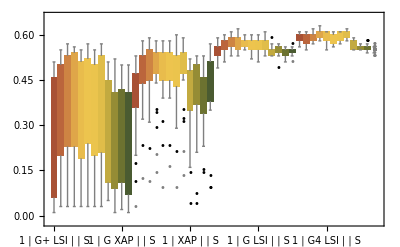

```mathematica
BoxWhiskerChart[
d[[All,All,2]],
"Outliers",
ChartStyle->"SandyTerrain",
ChartLabels->(Flatten[TagForMethods[#[[1]]]&/@ #&/@ d,1]),
PlotRange->{Automatic,Automatic},
ImageSize->Full]
```

## Comparing with and without stemming

```mathematica
bySeedSorted=SortBy[bySeed,Length[#]&];
```

```mathematica
Manipulate[
bySeedSorted[[i]][[All,{1,2,3,4,8,16,17,18,19,20,21,22,23,24,25,26,27}]]//MatrixForm
,{i,1,Length[bySeed],1}
]
```

Part::partd: Part specification bySeedSorted ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification bySeedSorted ⟦ 1 ⟧ ⟦ All, {1, 2, 3, 4, 8, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27} ⟧ is longer than depth of object.

## Comparing average precisions

```mathematica
{offset,prec,recall}={Partition[r[[10;;]],3][[All,1]],Partition[r[[10;;]],3][[All,2]],Partition[r[[10;;]],3][[All,3]]}
```

{{1,51,101,151,201,251,301,351,401,451,501,551,601,651,701,751,801,851,901,951,1001,1051},{1.,0.37,0.28,0.28,0.26,0.25,0.23,0.23,0.2,0.18,0.17,0.15,0.14,0.13,0.12,0.11,0.1,0.1,0.09,0.09,0.08,0.08},{0.01,0.23,0.34,0.51,0.64,0.75,0.84,0.95,0.96,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Total[Prepend[Differences[recall],recall[[1]]]*prec]
```

0.2863

```mathematica
Ap[r_]:= With[{parts=Partition[r[[10;;]],3]},
With[{recall=parts[[All,3]],prec=parts[[All,2]]},
Total[Prepend[Differences[recall],recall⟦1⟧]*prec]
]
]
```

```mathematica
Ap[relevant[[1]]]
```

0.3398

```mathematica
relevant[[1,8]]
```

LSI

```mathematica
byMethod=GatherBy [relevant,#[[{8,1,2,3}]]&];
apByMethod={#[[1,{8,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

```mathematica
Dimensions[apByMethod]
```

{12,2}

```mathematica
apByMethod[[All,1]]
```

{{LSI,-1,False,True},{LSI,2,False,True},{LSI,3,False,True},{LSI,3,True,True},{LSI,4,False,True},{LSI,False,False,True},{LSI,True,False,True},{LSI,True,True,True},{XAP,False,False,True},{XAP,False,True,True},{XAP,True,False,True},{XAP,True,True,True}}

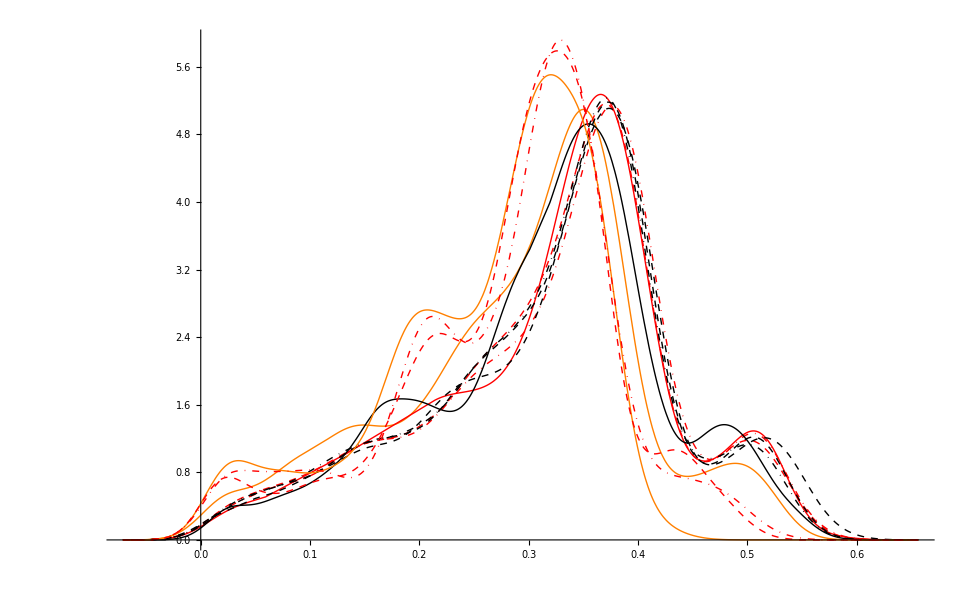

```mathematica
SmoothHistogram[{
Annotation[apByMethod[[1,2]],apByMethod[[1,1]],"Mouse"],
Annotation[apByMethod[[2,2]],apByMethod[[2,1]],"Mouse"],
Annotation[apByMethod[[3,2]],apByMethod[[3,1]],"Mouse"],
Annotation[apByMethod[[4,2]],apByMethod[[4,1]],"Mouse"],
Annotation[apByMethod[[5,2]],apByMethod[[5,1]],"Mouse"],
Annotation[apByMethod[[6,2]],apByMethod[[6,1]],"Mouse"],
Annotation[apByMethod[[7,2]],apByMethod[[7,1]],"Mouse"],
Annotation[apByMethod[[8,2]],apByMethod[[8,1]],"Mouse"],
Annotation[apByMethod[[9,2]],apByMethod[[9,1]],"Mouse"],
Annotation[apByMethod[[10,2]],apByMethod[[10,1]],"Mouse"],
Annotation[apByMethod[[11,2]],apByMethod[[11,1]],"Mouse"]
},Automatic,"PDF",
PlotStyle->{{Orange},{Red,Dashed},{Red,DotDashed},{Red},{Black,Dashed},{Black,Dashed},{Black,DotDashed},{Black}}
]
Dynamic[MouseAnnotation[]]
```

```mathematica
Sort[apByMethod][[All,1]]
```

{{LSI,250,True,True,True},{LSI,500,-1,False,True},{LSI,500,2,False,True},{LSI,500,3,False,True},{LSI,500,3,True,True},{LSI,500,4,False,True},{LSI,500,False,False,True},{LSI,500,True,False,True},{LSI,500,True,True,True},{XAP,100,False,False,True},{XAP,100,False,True,True},{XAP,100,True,False,True},{XAP,100,True,True,True}}

When restricting to small queries (<= 2)

```mathematica
smallQ=Select[relevant,#[[6]]≤5&];
byMethod=GatherBy [smallQ,#[[{8,9,1,2,3}]]&];
apByMethod={#[[1,{8,9,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

```mathematica
Length[#[[2]]]& /@ apByMethod
```

{391,511,511,511,511,511,511,511,511,510,510,510,510}

```mathematica
apByMethod[[1,1]]
```

{LSI,250,True,True,True}

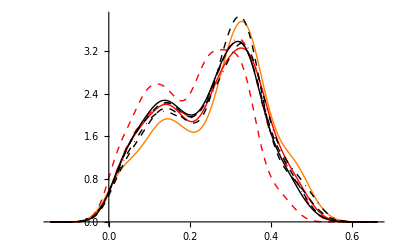

```mathematica
SmoothHistogram[{
Annotation[apByMethod[[1,2]],apByMethod[[1,1]],"Mouse"],
Annotation[apByMethod[[2,2]],apByMethod[[2,1]],"Mouse"],
Annotation[apByMethod[[3,2]],apByMethod[[3,1]],"Mouse"],
Annotation[apByMethod[[4,2]],apByMethod[[4,1]],"Mouse"],
Annotation[apByMethod[[5,2]],apByMethod[[5,1]],"Mouse"],
Annotation[apByMethod[[6,2]],apByMethod[[6,1]],"Mouse"],
Annotation[apByMethod[[7,2]],apByMethod[[7,1]],"Mouse"],
Annotation[apByMethod[[8,2]],apByMethod[[8,1]],"Mouse"]
},Automatic,"PDF",PlotStyle->{{Orange},{Red,Dashed},{Red,DotDashed},{Red},{Black,Dashed},{Black,Dashed},{Black,DotDashed},{Black}}]
Dynamic[MouseAnnotation[]]
```

## With and without genia

```mathematica
apByMethod[[All,1]]//MatrixForm
```

(LSI | -1 | False | True
LSI | 2 | False | True
LSI | 3 | False | True
LSI | 3 | True | True
LSI | 4 | False | True
LSI | False | False | True
LSI | True | False | True
LSI | True | True | True
XAP | False | False | True
XAP | False | True | True
XAP | True | False | True
XAP | True | True | True)

```mathematica
byMethod=GatherBy [relevant,#[[{8,1,2,3}]]&];
apByMethod={#[[1,{8,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

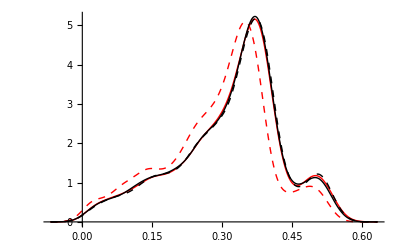

```mathematica
SmoothHistogram[{
Annotation[apByMethod[[1,2]],apByMethod[[1,1]],"Mouse"],
Annotation[apByMethod[[2,2]],apByMethod[[2,1]],"Mouse"],
Annotation[apByMethod[[5,2]],apByMethod[[5,1]],"Mouse"],
Annotation[apByMethod[[7,2]],apByMethod[[7,1]],"Mouse"]
},Automatic,"PDF",PlotStyle->{{Red,Dashed},{Red},{Black,Dashed},{Black}}]
Dynamic[MouseAnnotation[]]
```

## Comparing differences with a paired t-test over precision @ 200

```mathematica
prec200ByMethod={#[[1,{1,2,3,8}]],#[[All,23]]}&/@GatherBy[relevant,#[[{1,2,3,8}]]&];
```

```mathematica
Dimensions[prec200ByMethod]
```

{12,2}

```mathematica
{Mean[prec200ByMethod[[1,2]]],Median[prec200ByMethod[[1,2]]]}
{Mean[prec200ByMethod[[2,2]]],Median[prec200ByMethod[[2,2]]]}
```

{0.294841,0.32}

{0.31085,0.33}

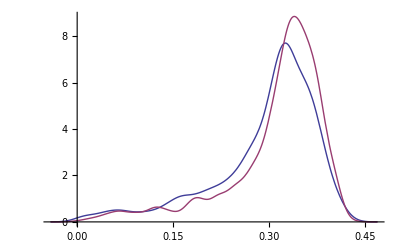

```mathematica
SmoothHistogram[{prec200ByMethod[[1,2]],prec200ByMethod[[2,2]]}]
```

```mathematica
KolmogorovSmirnovTest[prec200ByMethod[[1,2]],prec200ByMethod[[1,2]],{"TestDataTable","ShortTestConclusion"}]
```

{ | Statistic | P-Value
Kolmogorov-Smirnov | 0. | 1.,Do not reject}

```mathematica
{"TestDataTable","ShortTestConclusion"}
```

{TestDataTable,ShortTestConclusion}

```mathematica
Table[
{
If[Mean[prec200ByMethod[[i,2]]]< Mean[prec200ByMethod[[j,2]]],
KolmogorovSmirnovTest[prec200ByMethod[[i,2]],prec200ByMethod[[j,2]],"PValue"]
},
{i,1,Length[prec200ByMethod]},{j,1,Length[prec200ByMethod]}]//MatrixForm
```

((False
1.) | (False
0.) | (False
0.) | (False
0.00496454) | (False
0.) | (False
0.0151583) | (False
0.)
(True
0.) | (False
1.) | (True
1.77636×10^-15) | (True
0.) | (True
6.66134×10^-16) | (True
0.) | (True
0.)
(True
0.) | (False
1.77636×10^-15) | (False
1.) | (True
0.) | (False
0.0000307872) | (True
0.) | (True
0.000143365)
(True
0.00496454) | (False
0.) | (False
0.) | (False
1.) | (False
0.) | (True
0.00144959) | (False
1.50413×10^-12)
(True
0.) | (False
6.66134×10^-16) | (True
0.0000307872) | (True
0.) | (False
1.) | (True
0.) | (True
1.33227×10^-15)
(True
0.0151583) | (False
0.) | (False
0.) | (False
0.00144959) | (False
0.) | (False
1.) | (False
4.58111×10^-12)
(True
0.) | (False
0.) | (False
0.000143365) | (True
1.50413×10^-12) | (False
1.33227×10^-15) | (True
4.58111×10^-12) | (False
1.))

```mathematica
prec200ByMethod[[All,1]]
```

{{False,False,True,LSI},{False,False,True,XAP},{False,True,True,XAP},{True,False,True,LSI},{True,False,True,XAP},{True,True,True,LSI},{True,True,True,XAP}}

```mathematica
Quiet[TTest[{prec200ByMethod[[1,2]],prec200ByMethod[[,2]]},"PValue"]]
```

```mathematica
Table[
Quiet[TTest[{prec200ByMethod[[i,2]],prec200ByMethod[[j,2]]},Automatic,"PValue"]]
,
{i,1,Length[prec200ByMethod]},{j,1,Length[prec200ByMethod]}]//MatrixForm
```

(1. | 8.19337×10^-8 | 2.50994×10^-11 | 4.6955×10^-11 | 8.14203×10^-9 | 3.82989×10^-12 | 1.5889×10^-12 | 0.0171621 | 3.0935×10^-7 | 0.000136583 | 8.22887×10^-9 | 0.695711
8.19337×10^-8 | 1. | 0.158399 | 0.187858 | 0.644483 | 0.109499 | 2.89138×10^-36 | 6.5662×10^-15 | 0.82188 | 7.68729×10^-21 | 0.210655 | 1.23465×10^-8
2.50994×10^-11 | 0.158399 | 1. | 0.926758 | 0.346274 | 0.87079 | 2.81114×10^-43 | 1.17887×10^-19 | 0.104045 | 1.83209×10^-26 | 0.00259145 | 2.84848×10^-12
4.6955×10^-11 | 0.187858 | 0.926758 | 1. | 0.395703 | 0.797843 | 1.03141×10^-42 | 2.74902×10^-19 | 0.125415 | 5.0751×10^-26 | 0.00315905 | 5.42822×10^-12
8.14203×10^-9 | 0.644483 | 0.346274 | 0.395703 | 1. | 0.262032 | 3.79612×10^-38 | 2.99137×10^-16 | 0.495162 | 2.11023×10^-22 | 0.0640459 | 1.12824×10^-9
3.82989×10^-12 | 0.109499 | 0.87079 | 0.797843 | 0.262032 | 1. | 1.25801×10^-45 | 6.62961×10^-21 | 0.0690431 | 4.28597×10^-28 | 0.000929532 | 4.00369×10^-13
1.5889×10^-12 | 2.89138×10^-36 | 2.81114×10^-43 | 1.03141×10^-42 | 3.79612×10^-38 | 1.25801×10^-45 | 1. | 2.84922×10^-6 | 9.42252×10^-35 | 0.00071128 | 7.20502×10^-47 | 4.34769×10^-11
0.0171621 | 6.5662×10^-15 | 1.17887×10^-19 | 2.74902×10^-19 | 2.99137×10^-16 | 6.62961×10^-21 | 2.84922×10^-6 | 1. | 4.8289×10^-14 | 0.165858 | 3.43498×10^-19 | 0.0495008
3.0935×10^-7 | 0.82188 | 0.104045 | 0.125415 | 0.495162 | 0.0690431 | 9.42252×10^-35 | 4.8289×10^-14 | 1. | 9.52696×10^-20 | 0.339231 | 4.99023×10^-8
0.000136583 | 7.68729×10^-21 | 1.83209×10^-26 | 5.0751×10^-26 | 2.11023×10^-22 | 4.28597×10^-28 | 0.00071128 | 0.165858 | 9.52696×10^-20 | 1. | 7.3931×10^-26 | 0.000752849
8.22887×10^-9 | 0.210655 | 0.00259145 | 0.00315905 | 0.0640459 | 0.000929532 | 7.20502×10^-47 | 3.43498×10^-19 | 0.339231 | 7.3931×10^-26 | 1. | 3.87081×10^-10
0.695711 | 1.23465×10^-8 | 2.84848×10^-12 | 5.42822×10^-12 | 1.12824×10^-9 | 4.00369×10^-13 | 4.34769×10^-11 | 0.0495008 | 4.99023×10^-8 | 0.000752849 | 3.87081×10^-10 | 1.)

### Using CFP

```mathematica
CFP[d_,style_,label_]:=ListPlot[
Annotation[
Table[
{i,Length[Select[d,#≤i&]]/Length[d]},{i,Join[Range[0,1,0.05],Range[1,Max[d],1]]}
],label,"Mouse"]
,PlotRange->{{0,Max[d]*2},{0,1}},Joined->True,InterpolationOrder->0,PlotStyle->style]
```

```mathematica
Length[ColorData[35,"ColorList"]]
```

10

```mathematica
Rotate
```

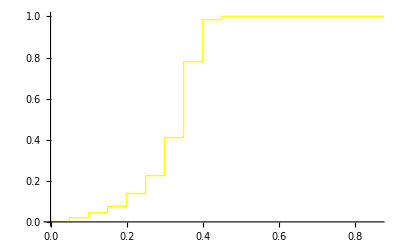

```mathematica
CFP[prec200ByMethod[[1,2]],Yellow,"Test"]
```

Part::partw: Part 11 of {RGBColor[0., 0., 0.], RGBColor[0.996078, 0.360784, 0.027451], RGBColor[0.996078, 0.988235, 0.0352941], RGBColor[0.541176, 0.713725, 0.027451], RGBColor[0.145098, 0.435294, 0.384314], RGBColor[0.00784314, 0.509804, 0.929412], RGBColor[0.152941, 0.113725, 0.490196], RGBColor[0.470588, 0.262745, 0.584314], RGBColor[0.890196, 0.0117647, 0.490196], RGBColor[0.905882, 0.027451, 0.129412]} does not exist.

Graphics::gprim: {RGBColor[0., 0., 0.], RGBColor[0.996078, 0.360784, 0.027451], RGBColor[0.996078, 0.988235, 0.0352941], RGBColor[0.541176, 0.713725, 0.027451], RGBColor[0.145098, 0.435294, 0.384314], RGBColor[0.00784314, 0.509804, 0.929412], RGBColor[0.152941, 0.113725, 0.490196], RGBColor[0.470588, 0.262745, 0.584314], RGBColor[0.890196, 0.0117647, 0.490196], RGBColor[0.905882, 0.027451, 0.129412]} ⟦ 11 ⟧ was encountered where a Graphics primitive or directive was expected.

Part::partw: Part 12 of {RGBColor[0., 0., 0.], RGBColor[0.996078, 0.360784, 0.027451], RGBColor[0.996078, 0.988235, 0.0352941], RGBColor[0.541176, 0.713725, 0.027451], RGBColor[0.145098, 0.435294, 0.384314], RGBColor[0.00784314, 0.509804, 0.929412], RGBColor[0.152941, 0.113725, 0.490196], RGBColor[0.470588, 0.262745, 0.584314], RGBColor[0.890196, 0.0117647, 0.490196], RGBColor[0.905882, 0.027451, 0.129412]} does not exist.

Graphics::gprim: {RGBColor[0., 0., 0.], RGBColor[0.996078, 0.360784, 0.027451], RGBColor[0.996078, 0.988235, 0.0352941], RGBColor[0.541176, 0.713725, 0.027451], RGBColor[0.145098, 0.435294, 0.384314], RGBColor[0.00784314, 0.509804, 0.929412], RGBColor[0.152941, 0.113725, 0.490196], RGBColor[0.470588, 0.262745, 0.584314], RGBColor[0.890196, 0.0117647, 0.490196], RGBColor[0.905882, 0.027451, 0.129412]} ⟦ 12 ⟧ was encountered where a Graphics primitive or directive was expected.

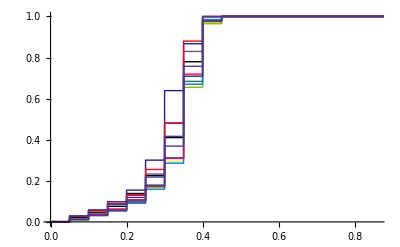

```mathematica
Show[
Table[
CFP[prec200ByMethod[[i,2]],{ColorData[3,"ColorList"][[i]]},prec200ByMethod[[i,1]]],
{i,1,Length[prec200ByMethod]}
]
]
Dynamic[MouseAnnotation[]]
```

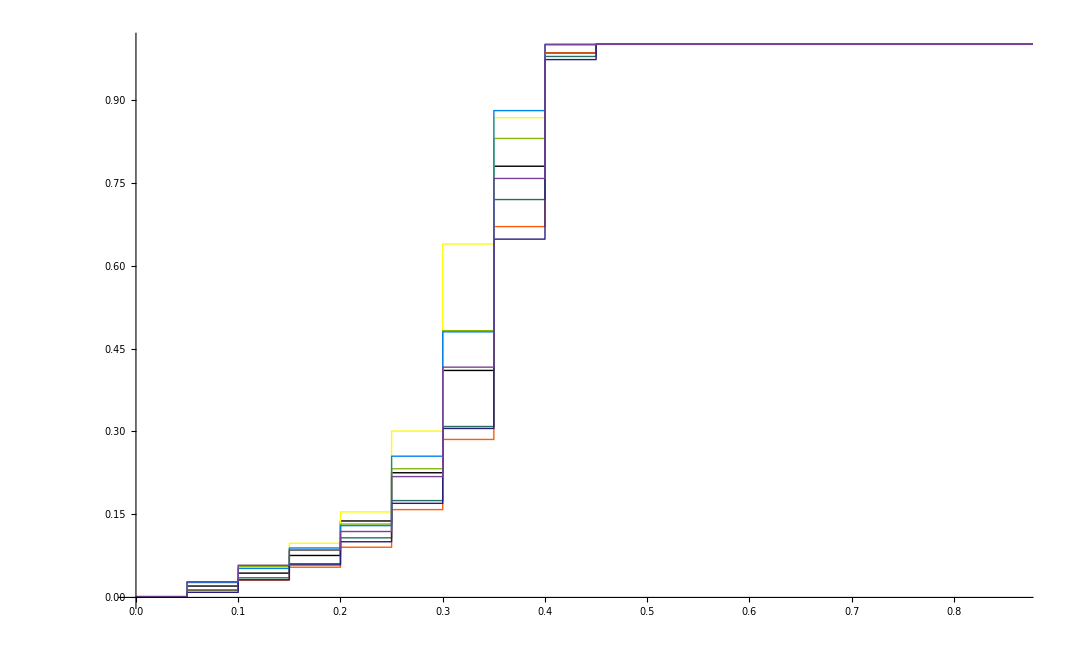

## What’s the mean average precision per method ?

```mathematica
byMethod=GatherBy [relevant,#[[{8,9,1,2,3}]]&];
apByMethod={#[[1,{8,9,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

```mathematica
Dimensions[apByMethod]
```

{16,2}

```mathematica
apByMethod[[All,1]]//MatrixForm
```

(LSI | 100 | True | True | True
LSI | 250 | True | True | True
LSI | 500 | -1 | False | True
LSI | 500 | 2 | False | True
LSI | 500 | 3 | False | True
LSI | 500 | 3 | True | True
LSI | 500 | 4 | False | True
LSI | 500 | False | False | True
LSI | 500 | True | False | True
LSI | 500 | True | True | True
LSI | 750 | True | True | True
LSI | 1000 | True | True | True
XAP | 100 | False | False | True
XAP | 100 | False | True | True
XAP | 100 | True | False | True
XAP | 100 | True | True | True)

```mathematica
SortBy[{#[[1]],Mean[#[[2]]]}&/@ apByMethod,#[[2]]&]//MatrixForm
```

({XAP,100,False,False,True} | 0.262492
{XAP,100,True,False,True} | 0.280183
{XAP,100,False,True,True} | 0.283452
{LSI,500,-1,False,True} | 0.291768
{XAP,100,True,True,True} | 0.292124
{LSI,100,True,True,True} | 0.300317
{LSI,1000,True,True,True} | 0.301393
{LSI,250,True,True,True} | 0.311465
{LSI,500,True,False,True} | 0.317002
{LSI,500,2,False,True} | 0.31769
{LSI,500,True,True,True} | 0.318974
{LSI,500,4,False,True} | 0.319459
{LSI,500,3,True,True} | 0.321054
{LSI,500,3,False,True} | 0.322525
{LSI,750,True,True,True} | 0.324396
{LSI,500,False,False,True} | 0.325772)

```mathematica
styles=Switch[#[[1,{1,2}]],{"XAP",100},Black,{"LSI",500},Red,{"LSI",250},Orange,{"LSI",750},{Red,Thick},{"LSI",100},{Red,Dashed},{"LSI",1000},{Red,Thick,Dashed}]&/@ apByMethod;
```

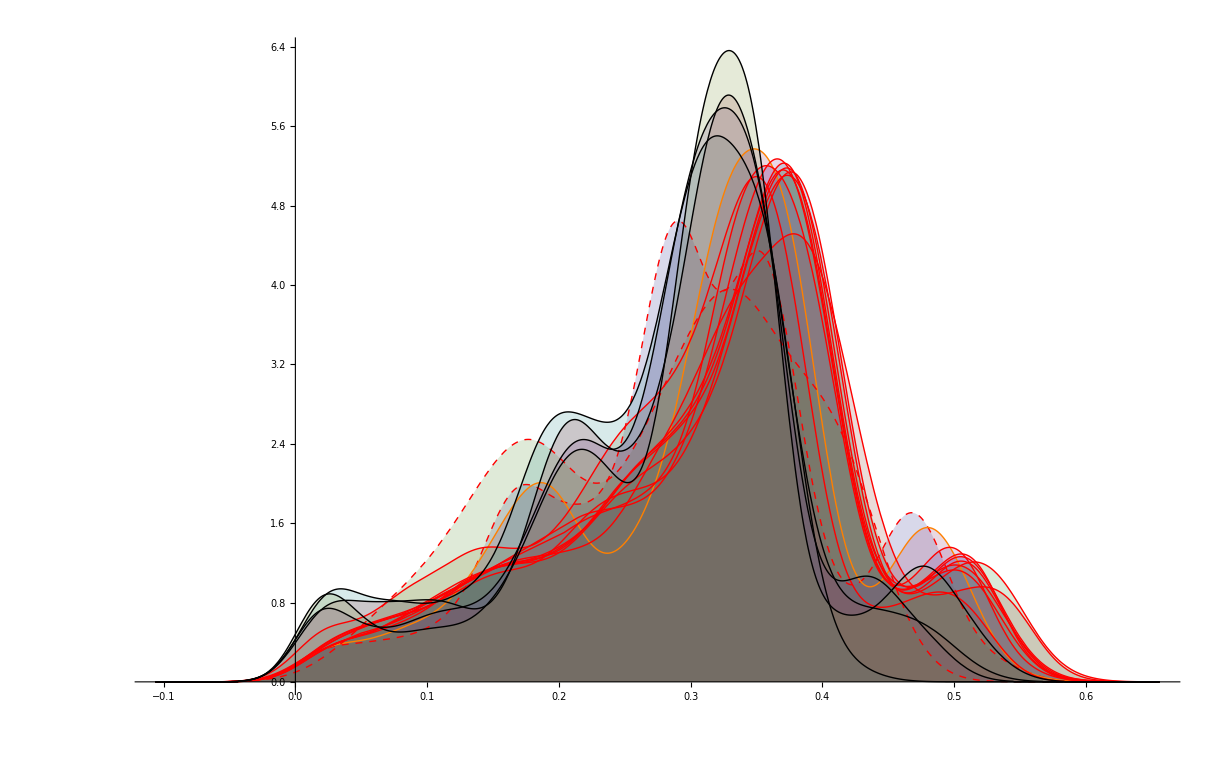

```mathematica
SmoothHistogram[
Table[Annotation[apByMethod[[i,2]],apByMethod[[i,1]],"Mouse"],{i,1,Length[apByMethod]}]
,Automatic,PlotStyle->styles,Filling->Bottom]
Dynamic[MouseAnnotation[]]
```

## Mean F1 score at fixed cut-of values

```mathematica
Table[{relevant[[1,i]],{"prec",i+1,"reC",i+2}},{i,Range[10,75,3]}]//MatrixForm
```

(1 | {prec,11,reC,12}
51 | {prec,14,reC,15}
101 | {prec,17,reC,18}
151 | {prec,20,reC,21}
201 | {prec,23,reC,24}
251 | {prec,26,reC,27}
301 | {prec,29,reC,30}
351 | {prec,32,reC,33}
401 | {prec,35,reC,36}
451 | {prec,38,reC,39}
501 | {prec,41,reC,42}
551 | {prec,44,reC,45}
601 | {prec,47,reC,48}
651 | {prec,50,reC,51}
701 | {prec,53,reC,54}
751 | {prec,56,reC,57}
801 | {prec,59,reC,60}
851 | {prec,62,reC,63}
901 | {prec,65,reC,66}
951 | {prec,68,reC,69}
1001 | {prec,71,reC,72}
1051 | {prec,74,reC,75})

We cut at 100 documents

```mathematica
precI=20;recI=21;
f1scores={#[[3;;]],If[#[[1]]+#[[2]]==0,0,(2*#[[1]]*#[[2]])/(#[[1]]+#[[2]])]}&/@relevant[[All,{precI,recI,8,9,1,2,3}]];
byMeth=GatherBy[f1scores,#[[1,{1,2,3,4,5}]]&];
f1ByMeth=Table[byMeth[[i,1,1]]-> Mean[Select[byMeth[[i,All,2]],#≠0&]],{i,1,Length[byMeth]}];
SortBy[f1ByMeth,#[[2]]&]//MatrixForm
```

({XAP,100,False,False,True}→0.339413
{XAP,100,True,False,True}→0.352187
{XAP,100,False,True,True}→0.353107
{XAP,100,True,True,True}→0.361767
{LSI,500,-1,False,True}→0.375762
{LSI,100,True,True,True}→0.376788
{LSI,250,True,True,True}→0.391582
{LSI,500,True,False,True}→0.39747
{LSI,500,2,False,True}→0.39894
{LSI,500,4,False,True}→0.399257
{LSI,500,True,True,True}→0.399575
{LSI,500,3,True,True}→0.399716
{LSI,750,True,True,True}→0.402835
{LSI,500,3,False,True}→0.403369
{LSI,500,False,False,True}→0.405128)

```mathematica
Dimensions[byMeth]
```

{15}

```mathematica
byMeth[[1]]
```

{{{LSI,500,-1,False,True},0.436632},{{LSI,500,-1,False,True},0.361519},{{LSI,500,-1,False,True},0.436632},{{LSI,500,-1,False,True},0.30806},{{LSI,500,-1,False,True},0.321429},{{LSI,500,-1,False,True},0.412444},{{LSI,500,-1,False,True},0.388235},«1398»,{{LSI,500,-1,False,True},0.594462},{{LSI,500,-1,False,True},0.610299},{{LSI,500,-1,False,True},0.583594},{{LSI,500,-1,False,True},0.594462},{{LSI,500,-1,False,True},0.567742},{{LSI,500,-1,False,True},0.610299}}

```mathematica
Length/@byMeth
```

{1411,1411,1411,1411,1411,1411,1410,1410,1411,1410,1411,1411,1411,1411,1410}

```mathematica
byMeth[[1,1,1,{1,2}]]
```

{LSI,500}

```mathematica
styles=Switch[#[[1,1,{1,2}]],{"XAP",100},Black,{"LSI",500},Red,{"LSI",250},Orange,{"LSI",750},{Red,Thick,Dashed},{"LSI",100},{Red,Dashed}]&/@ byMeth
```

{RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],GrayLevel[0],GrayLevel[0],RGBColor[1,0,0],GrayLevel[0],{RGBColor[1,0,0],Dashing[{Small,Small}]},RGBColor[1,0.5,0],RGBColor[1,0,0],{RGBColor[1,0,0],Thickness[Large],Dashing[{Small,Small}]},GrayLevel[0]}

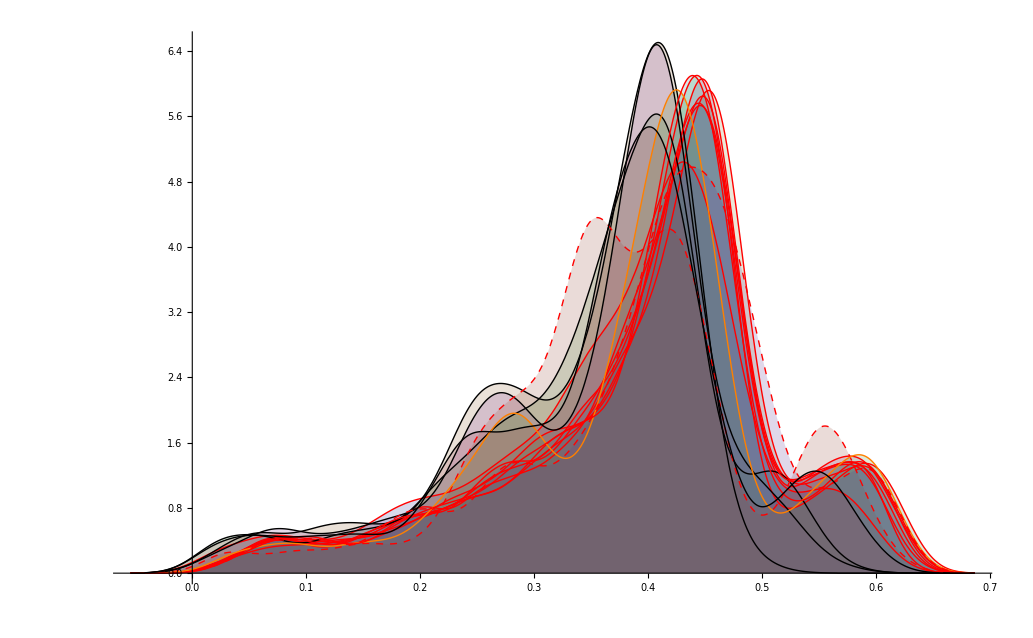

```mathematica
SmoothHistogram[
Table[Annotation[
Select[byMeth[[i,All,2]],#≠0&],
byMeth[[i,1,1]],"Mouse"],{i,1,Length[byMeth]}]
,Automatic,PlotStyle->styles,Filling->Bottom]
Dynamic[MouseAnnotation[]]
```

```mathematica
byMeth[[1,1,1]]
```

{LSI,500,-1,False,True}

```mathematica
TagForMethodsF1[m_]:= 
Style[Grid[Transpose[{{m[[1]], "", m[[2]]}, {Switch[m[[3]],"False","",-1,"G+","True","G",_,"G"<>ToString[m[[3]]]], If[m[[4]]=="True","M",""], If[m[[5]]=="True","S",""]}}],Frame->LightGray],FontSize->8]
```

```mathematica
byMeth[[All,1,1]]
```

{{LSI,500,-1,False,True},{LSI,500,2,False,True},{LSI,500,3,False,True},{LSI,500,3,True,True},{LSI,500,4,False,True},{LSI,500,False,False,True},{XAP,100,False,False,True},{XAP,100,False,True,True},{LSI,500,True,False,True},{XAP,100,True,False,True},{LSI,100,True,True,True},{LSI,250,True,True,True},{LSI,500,True,True,True},{LSI,750,True,True,True},{XAP,100,True,True,True}}

```mathematica
TagForMethodsF1 /@ byMeth[[All,1,1]]
```

{LSI | G+
 | 
500 | S,LSI | G2
 | 
500 | S,LSI | G3
 | 
500 | S,LSI | G3
 | M
500 | S,LSI | G4
 | 
500 | S,LSI | 
 | 
500 | S,XAP | 
 | 
100 | S,XAP | 
 | M
100 | S,LSI | G
 | 
500 | S,XAP | G
 | 
100 | S,LSI | G
 | M
100 | S,LSI | G
 | M
250 | S,LSI | G
 | M
500 | S,LSI | G
 | M
750 | S,XAP | G
 | M
100 | S}

```mathematica
Dimensions[Select[#[[All,2]],#≠0&]&/@ byMeth]
```

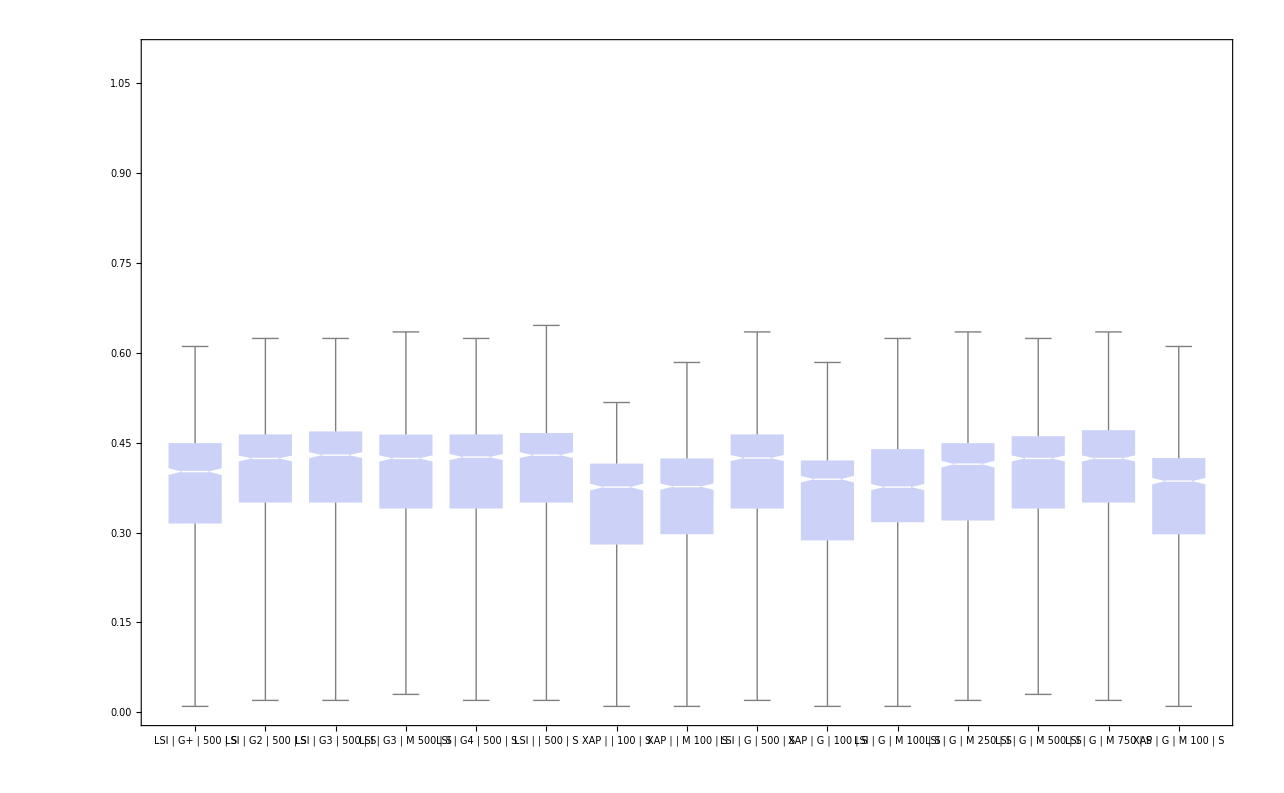

```mathematica
BoxWhiskerChart[
Select[#[[All,2]],#≠0&]&/@ byMeth,
"Notched",
ChartLabels->TagForMethodsF1 /@ byMeth[[All,1,1]],
PlotRange->{Automatic,{0,1.1}}
]
```

## Global comparison using t-tests cannot be performed due to the non normality of the distributions

Is this non normality due to different pathways?

```mathematica
relevant[[100]]
```

{-1,False,True,False,2,8,{8643607,8798622,9162033,10809237,11071847,11719514,15994236,17192406},LSI,500,1,1.,0.01,51,0.43,0.27,101,0.38,0.46,151,0.35,0.64,201,0.32,0.77,251,0.31,0.93,301,0.27,0.96,351,0.23,0.98,401,0.2,0.98,451,0.18,0.99,501,0.16,0.99,551,0.15,0.99,601,0.14,0.99,651,0.13,0.99,701,0.12,0.99,751,0.11,1.,801,0.1,1.,851,0.1,1.,901,0.09,1.,951,0.09,1.,1001,0.08,1.,1051,0.08,1.}

```mathematica
precI=20;recI=21;
f1scores={#[[3;;]],If[#[[1]]+#[[2]]==0,0,(2*#[[1]]*#[[2]])/(#[[1]]+#[[2]])]}&/@relevant[[All,{precI,recI,8,9,1,2,3,5,6}]];
```

```mathematica
byPathAndMeth=GatherBy[f1scores,#[[1,{1,2,3,4,5,6,7}]]&];
```

```mathematica
f1scores[[100]]
```

{{LSI,500,-1,False,True,2,8},0.452525}

```mathematica
Length[byPathAndMeth]
```

720

```mathematica
byPathAndMeth[[1,All]]
```

{{{LSI,500,-1,False,True,2,1},0.436632},{{LSI,500,-1,False,True,2,1},0.361519},{{LSI,500,-1,False,True,2,1},0.436632},{{LSI,500,-1,False,True,2,1},0.30806},{{LSI,500,-1,False,True,2,1},0.321429},{{LSI,500,-1,False,True,2,1},0.412444},{{LSI,500,-1,False,True,2,1},0.388235},{{LSI,500,-1,False,True,2,1},0.414945},{{LSI,500,-1,False,True,2,1},0.385714},{{LSI,500,-1,False,True,2,1},0.30806},{{LSI,500,-1,False,True,2,1},0.412444},{{LSI,500,-1,False,True,2,1},0.436632},{{LSI,500,-1,False,True,2,1},0.388235},{{LSI,500,-1,False,True,2,1},0.401591},{{LSI,500,-1,False,True,2,1},0.436632},{{LSI,500,-1,False,True,2,1},0.385714},{{LSI,500,-1,False,True,2,1},0.412444},{{LSI,500,-1,False,True,2,1},0.297231},{{LSI,500,-1,False,True,2,1},0.385714},{{LSI,500,-1,False,True,2,1},0.412444},{{LSI,500,-1,False,True,2,1},0.206222},{{LSI,500,-1,False,True,2,1},0.412444},{{LSI,500,-1,False,True,2,1},0.385714},{{LSI,500,-1,False,True,2,1},0.388235},{{LSI,500,-1,False,True,2,1},0.0133333}}

```mathematica
byMethAndQSize=GatherBy[f1scores,#[[1,{1,2,3,4,5,7}]]&];
f1ByQSize=Table[byMethAndQSize[[i,1,1]]-> byMethAndQSize[[i,All,2]],{i,1,Length[byMethAndQSize]}];
```

```mathematica
f1ByPathAndMeth=Table[byPathAndMeth[[i,1,1]]-> byPathAndMeth[[i,All,2]],{i,1,Length[byPathAndMeth]}];
```

```mathematica
f1ByPathAndMeth[[30]]
```

{LSI,500,-1,False,True,9,16}→{0.456522,0.41619,0.436364,0.351549,0.470737,0.375789,0.391899,0.371733,0.375789,0.381818,0.480825,0.371733,0.351549,0.436364,0.396,0.381818,0.456522,0.406098,0.41619,0.396,0.396,0.406098,0.391899,0.490909,0.41619,0.41619,0.450549,0.371733,0.426279,0.381818}

```mathematica
f1ByPathAndMeth[[1]]
```

{LSI,500,-1,False,True,2,1}→{0.436632,0.361519,0.436632,0.30806,0.321429,0.412444,0.388235,0.414945,0.385714,0.30806,0.412444,0.436632,0.388235,0.401591,0.436632,0.385714,0.412444,0.297231,0.385714,0.412444,0.206222,0.412444,0.385714,0.388235,0.0133333}

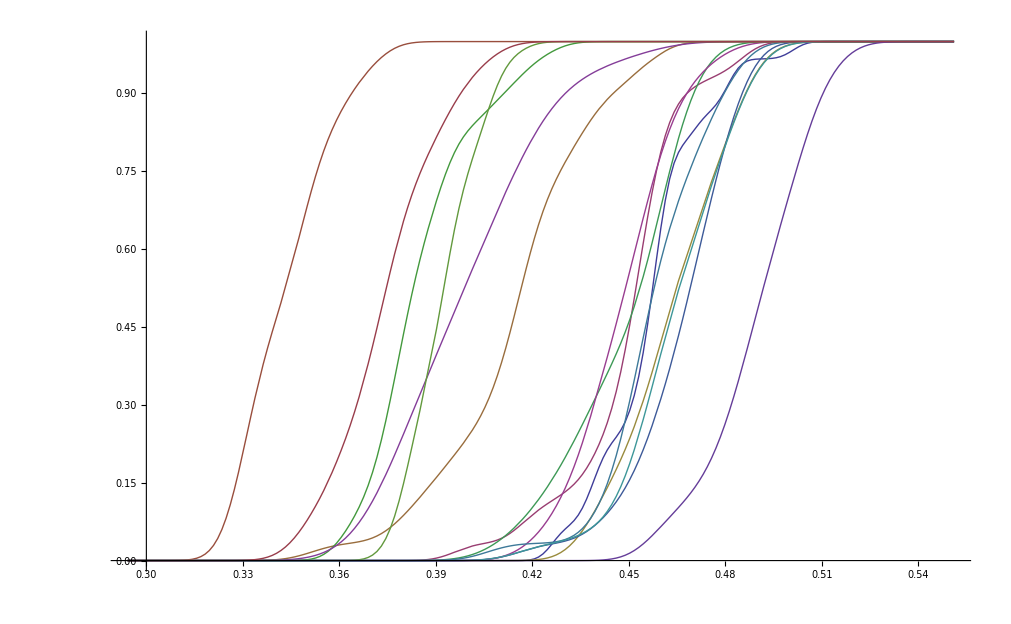

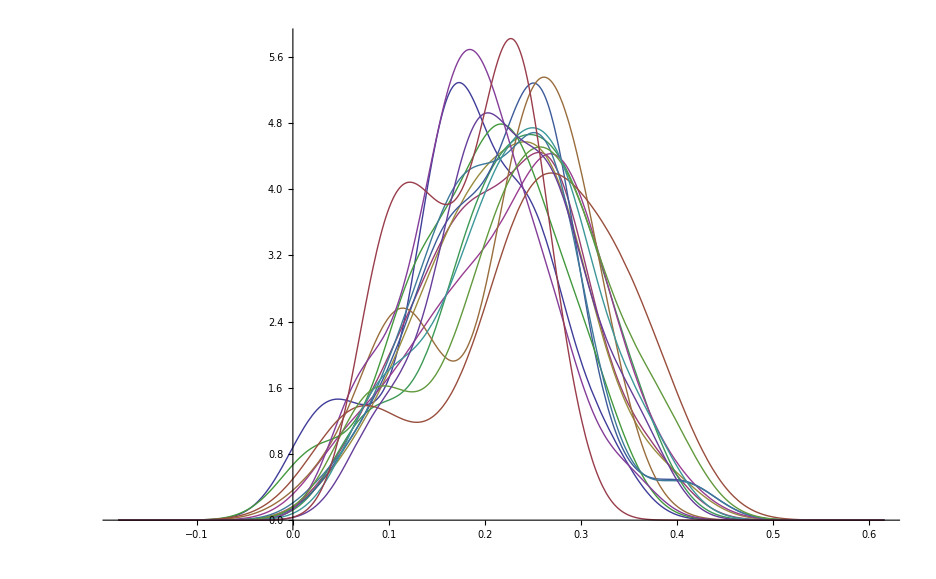

```mathematica
pw=9;
qSize=62;
thisPw=Select[f1ByPathAndMeth,(#[[1,6]]==pw)∧(#[[1,7]]==qSize)&];
SmoothHistogram[
Table[
Annotation[thisPw[[i,2]],thisPw[[i,1]],"Mouse"],{i,1,Length[thisPw]}],
Automatic,"CDF"]
Dynamic[MouseAnnotation[]]
```

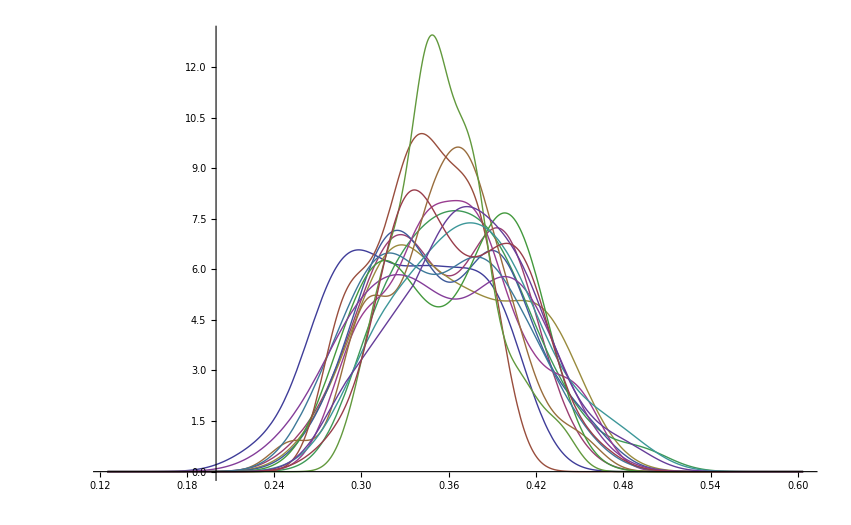

```mathematica
Length /@ thisPw[[All,2]]
```

{}

```mathematica
thisPw=Select[f1ByPathAndMeth,((#[[1,6]]==pw)∧(#[[1,7]]==qSize))&]
```

{}

```mathematica
f1ByPathAndMeth[[All,All,1]]
```

{LSI→0.436632,LSI→0.17,LSI→0.02,LSI→0.163636,LSI→0.252549,LSI→0.401591,LSI→0.436632,LSI→0.19,LSI→0.03,LSI→0.203902,LSI→0.276786,LSI→0.364,LSI→0.452525,LSI→0.2,LSI→0.03,LSI→0.203902,LSI→0.280702,LSI→0.339733,LSI→0.436632,LSI→0.17,LSI→0.03,LSI→0.2484,LSI→0.335294,LSI→0.350649,LSI→0.441649,LSI→0.184865,LSI→0.03,LSI→0.203902,LSI→0.290847,LSI→0.339733,LSI→0.452525,XAP→0.348158,LSI→0.17,XAP→0.21,LSI→0.03,XAP→0.05,LSI→0.2484,XAP→0.297,LSI→0.355556,XAP→0.335294,LSI→0.337297,XAP→0.166111,XAP→0.374878,XAP→0.07,XAP→0.01,XAP→0.297,XAP→0.311111,XAP→0.192857,LSI→0.441649,XAP→0.401591,LSI→0.18,XAP→0.164848,LSI→0.03,XAP→0.01,LSI→0.198,XAP→0.208095,LSI→0.280702,XAP→0.311111,LSI→0.323944,XAP→0.182,LSI→0.452525,LSI→0.436632,LSI→0.414945,LSI→0.425806,XAP→0.323944,LSI→0.21,LSI→0.19,LSI→0.19,LSI→0.18,XAP→0.16,LSI→0.03,LSI→0.03,LSI→0.03,LSI→0.02,XAP→0.01,LSI→0.252549,LSI→0.262642,LSI→0.23234,LSI→0.208095,XAP→0.238333,LSI→0.290847,LSI→0.355556,LSI→0.335294,LSI→0.315,XAP→0.290847,LSI→0.401591,LSI→0.401591,LSI→0.364,LSI→0.337297,XAP→0.217021}

```mathematica
qSize=10;
Manipulate[
thisPw=Select[f1ByQSize,(#[[1,7]]==qSize)&];
SmoothHistogram[
Table[
Annotation[thisPw[[i,2]],thisPw[[i,1]],"Mouse"],{i,1,Length[thisPw]}],
Automatic,"CDF"]
,{qSize,{1,2,5,8,10,16,41,62}}
]
Dynamic[MouseAnnotation[]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[f1ByQSize, #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 &].

Part::partd: Part specification Select[f1ByQSize, #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 &] ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification Select[f1ByQSize, #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 &] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partw: Part 2 of #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 & does not exist.

Part::partd: Part specification #1 ⟦ 1, 7 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

SmoothHistogram::ldata: {Select[f1ByQSize, #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 &] ⟦ 1, 2 ⟧, Select[f1ByQSize, #1 ⟦ 1, 7 ⟧ == FE`qSize$$6 &] ⟦ 2, 2 ⟧} is not a valid dataset or list of datasets.

## Comparing AP distributions with the T-test

```mathematica
byMethod=GatherBy [relevant,#[[{8,9,1,2,3}]]&];
apByMethod={#[[1,{8,9,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

Successive t-test over ranked average values

```mathematica
SortBy[{#[[1]],Mean[#[[2]]]}&/@ apByMethod,#[[2]]&]//MatrixForm
```

({XAP,100,False,False,True} | 0.262492
{XAP,100,True,False,True} | 0.280183
{XAP,100,False,True,True} | 0.283452
{LSI,500,-1,False,True} | 0.291768
{XAP,100,True,True,True} | 0.292124
{LSI,100,True,True,True} | 0.300317
{LSI,250,True,True,True} | 0.311465
{LSI,500,True,False,True} | 0.317002
{LSI,500,2,False,True} | 0.31769
{LSI,500,True,True,True} | 0.318974
{LSI,500,4,False,True} | 0.319459
{LSI,500,3,True,True} | 0.321054
{LSI,500,3,False,True} | 0.322525
{LSI,750,True,True,True} | 0.324396
{LSI,500,False,False,True} | 0.325772
{LSI,1000,True,True,True} | 0.326775)

```mathematica
sortedApByMethod=SortBy[apByMethod,Mean[#[[2]]]&];
```

```mathematica
Table[Prepend[sortedApByMethod[[i,1]],i],{i,1,Length[sortedApByMethod]}]//MatrixForm
```

(1 | XAP | 100 | False | False | True
2 | XAP | 100 | True | False | True
3 | XAP | 100 | False | True | True
4 | LSI | 500 | -1 | False | True
5 | XAP | 100 | True | True | True
6 | LSI | 100 | True | True | True
7 | LSI | 250 | True | True | True
8 | LSI | 500 | True | False | True
9 | LSI | 500 | 2 | False | True
10 | LSI | 500 | True | True | True
11 | LSI | 500 | 4 | False | True
12 | LSI | 500 | 3 | True | True
13 | LSI | 500 | 3 | False | True
14 | LSI | 750 | True | True | True
15 | LSI | 500 | False | False | True
16 | LSI | 1000 | True | True | True)

```mathematica
TTest[{apByMethod[[10,2]],apByMethod[[14,2]]},Automatic,{"TestDataTable","ShortTestConclusion","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "T", "Z", "KSampleT"} ∩ "T".

{ | Statistic | P-Value
T | 8.96524 | 5.54819×10^-19,Reject,The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the T test.}

```mathematica
comparisons=Table[
TTest[{sortedApByMethod[[i,2]],sortedApByMethod[[i+1,2]]},Automatic,{"ShortTestConclusion"}],{i,1,Length[sortedApByMethod]-1}
]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{{Reject},{Do not reject},{Reject},{Do not reject},{Reject},{Reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject},{Do not reject}}

```mathematica
{sortedApByMethod[[All,1]]//MatrixForm,comparisons//MatrixForm}
```

{(XAP | 100 | False | False | True
XAP | 100 | True | False | True
XAP | 100 | False | True | True
LSI | 500 | -1 | False | True
XAP | 100 | True | True | True
LSI | 100 | True | True | True
LSI | 250 | True | True | True
LSI | 500 | True | False | True
LSI | 500 | 2 | False | True
LSI | 500 | True | True | True
LSI | 500 | 4 | False | True
LSI | 500 | 3 | True | True
LSI | 500 | 3 | False | True
LSI | 750 | True | True | True
LSI | 500 | False | False | True
LSI | 1000 | True | True | True),(Reject
Do not reject
Reject
Do not reject
Reject
Reject
Do not reject
Do not reject
Do not reject
Do not reject
Do not reject
Do not reject
Do not reject
Do not reject
Do not reject)}